## Tutorial: Flat-bands, hyperbolic Lieb lattice

This is a notebook for the first steps for the use of the HyperBloch package for efficient modeling of tight-binding models on hyperbolic lattices.

## Preliminaries:

### Remark:

Before using the getting started with the HyperBloch notebook:

Make sure that the HyperBloch package is installed, if this is not the case please follow the instruction on the website (link to website ???).

Make sure that the required files .hcc,  .hcm and .hcs files are in the current directory. This entails files:

(2,4,6)_T2.2_3.hcc

{6,4}-Lieb_T2.2_3.hcm

{6,4}-Lieb_T2.2_3_sc-T5.4.hcs

{6,4}-Lieb_T2.2_3_sc-T9.3.hcs

In case no such files exists, please follow the instructions in the the prerequisites section on the website (link to website ???) or download it there.

### Load the HyperBloch package:

```mathematica
<<PatrickMLenggenhager`HyperBloch`
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Open the documentation:

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/tutorial/BasicUsage"];
```

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/guide/HyperBlochPackage"];
```

### Needed functions:

```mathematica
ComputeEigenvalues[cfH_,Npts_,Nruns_,genus_]:=
Flatten@ParallelTable[
Flatten@Table[
Eigenvalues[cfH@@RandomReal[{-Pi,Pi},2genus]],{i,1,Round[Npts/Nruns]}],
{j,1,Nruns},Method->"FinestGrained"]
```

## {6,4} Lieb lattice:

### Import cells

We first import the cell, model, and supercell model graphs as produced by the HyperCells package:

We consider the following sequence of supercells, defined in terms of quotients given in https://www.math.auckland.ac.nz/~conder/TriangleGroupQuotients101.txt by M. Conder, (the cell “T2.6” is the primitive cell):

```mathematica
cellsLieb={"T2.2","T5.4","T9.3"}; 
genusLstLieb={2,5,9};
```

Cell graph:

```mathematica
pcellLieb=ImportCellGraphString[Import["(2,4,6)_T2.2_3.hcc"]];
```

Primitive cell:

```mathematica
pcmodelLieb=ImportModelGraphString[Import["{6,4}-Lieb_T2.2_3.hcm"]];
```

Visualize the model graph:

```mathematica
VisualizeModelGraph[pcmodelLieb,
Elements-><|
			ShowCellGraphFlattened->{},
			ShowCellBoundary->{ShowEdgeIdentification->True}
		|>,

CellGraph->pcellLieb,
NumberOfGenerations->3,
ImageSize->400]
```

Det::luc: Result for Det of badly conditioned matrix {{0.358719,-0.207107},{0.612372,-0.353553}} may contain significant numerical errors.

Det::luc: Result for Det of badly conditioned matrix {{0.358719,0.207107},{0.612372,0.353553}} may contain significant numerical errors.

Det::luc: Result for Det of badly conditioned matrix {{0.408248,-0.707107},{0.258819,-0.448288}} may contain significant numerical errors.

General::stop: Further output of Det::luc will be suppressed during this calculation.

-Graphics-

Supercells:

```mathematica
scmodelsLieb=Association[#->
ImportSupercellModelGraphString[ 
Import[ToString@StringForm["{6,4}-Lieb_T2.2_3_sc-``.hcs",#]]]
&/@cellsLieb[[2;;]]];
```

### Hamiltonian:

Primitive cell:

The Hamiltonian for the nearest-neighbor tight-binding model on the primitive cell T2.2 is:

```mathematica
HpcLieb=AbelianBlochHamiltonian[pcmodelLieb,1,0&,-1&,CompileFunction->True];
```

Supercells:

The Hamiltonians for the nearest - neighbor tight - binding model on the sequence of supercells are, (this might take a minute):

```mathematica
HclstLieb=
Join[Association["T2.2"->HpcLieb],
Association[#->
AbelianBlochHamiltonian[scmodelsLieb[#],1,0&,-1&,PCModel->pcmodelLieb,CompileFunction->True]
&/@cellsLieb[[2;;]]]];
```

### Density of states:

Let us compute the density of states by exact diagonalization.

Compute the Eigenvalues via 10^4 momentum random samples, (this might take a minute):

```mathematica
evalsLieb=Association[cellsLieb[[#]]->ComputeEigenvalues[HclstLieb[cellsLieb[[#]]],  10^4,32,genusLstLieb[[#]]]&/@Range[3]];
```

Visualize density of states via a kernel density estimation, (this might take a minute):

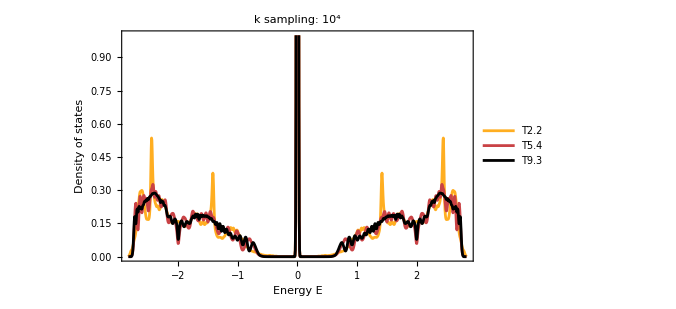

```mathematica
SmoothHistogram[evalsLieb,0.01,"PDF",Frame->True,FrameStyle->Black,FrameLabel->{"Energy E","Density of states"},PlotRange->{0,1}, LabelStyle->20,PlotLabel->"k sampling: 10^4",PlotStyle->(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,3]/3.)),ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},Background->None]
```

```mathematica
NotebookSave[]
```